```mathematica
ClearAll[fNL,b,ns,F,LogL,w,degRes,lmax,cμT,cTT,cμμN,σ]

b = 1+12.1(ns-1)
nsfid=0.965
bfid =1+12.1(nsfid-1)
fNLfid = 25000
w = (2.0*10^(-9))^(-2)
degRes=1.6*Pi/180
lmax =Sqrt[8*Log[2]]/degRes
prior =DiagonalMatrix[{0,1/.004^2}]

cμT[l_] := 2.2*10^(-16)*fNL*b/(l(l+1))
(*cTT[l_] := 6.0*10^(-10)*1/(l(l+1))*)
cTT[l_]:=cttCAMBindx[[l+1]]
cμμN[l_] :=w^(-1)*Exp[(l/lmax)^2]

σ[l_]:=Sqrt[1/(2l+1)*cTT[l]*cμμN[l]]
LogL=(1/2)Sum[cμT[q]*cμT[q]/(σ[q]^2),{q,2,lmax}]
```

1+12.1 (-1+ns)

0.965

0.5765

25000

2.5×10^17

0.0279253

84.3258

{{0.,0.},{0.,62500.}}

0.0000497435 fNL^2 (1+12.1 (-1+ns))^2

```mathematica
n = 2
params = {fNL,ns}
FDLogL = Table[Sum[D[cμT[q],params[[x]]]*D[cμT[q],params[[y]]]/(σ[q]^2),{q,2,lmax}],{x,1,n},{y,1,n}]+prior
(*Fnd = Table[D[LogL,params[[x]]]*D[LogL,params[[y]]],{x,1,n},{y,1,n}]*)
Fnd = Table[D[D[LogL,params[[x]]],params[[y]]],{x,1,n},{y,1,n}]+prior
```

2

{fNL,ns}

{{0.+0.0000994869 (1+12.1 (-1+ns))^2,0.+0.00120379 fNL (1+12.1 (-1+ns))},{0.+0.00120379 fNL (1+12.1 (-1+ns)),62500.+0.0145659 fNL^2}}

{{0.+0.0000994869 (1+12.1 (-1+ns))^2,0.+0.00240758 fNL (1+12.1 (-1+ns))},{0.+0.00240758 fNL (1+12.1 (-1+ns)),62500.+0.0145659 fNL^2}}

```mathematica
Det[Fnd]/.{ns->nsfid,fNL ->fNLfid}
Finv = Inverse[Fnd]
```

-900.965

{{(62500.+0.0145659 fNL^2)/(766.112-0.000535636 fNL^2-1670.26 ns+0.00116778 fNL^2 ns+910.368 ns^2-0.000636495 fNL^2 ns^2),(0.-0.00240758 fNL (1+12.1 (-1+ns)))/(766.112-0.000535636 fNL^2-1670.26 ns+0.00116778 fNL^2 ns+910.368 ns^2-0.000636495 fNL^2 ns^2)},{(0.-0.00240758 fNL (1+12.1 (-1+ns)))/(766.112-0.000535636 fNL^2-1670.26 ns+0.00116778 fNL^2 ns+910.368 ns^2-0.000636495 fNL^2 ns^2),(0.+0.0000994869 (1+12.1 (-1+ns))^2)/(766.112-0.000535636 fNL^2-1670.26 ns+0.00116778 fNL^2 ns+910.368 ns^2-0.000636495 fNL^2 ns^2)}}

```mathematica
UmFnlFloor= 1/Sqrt[Fnd[[1,1]]] /.ns->nsfid
UmnsFloor =  1/Sqrt[Fnd[[2,2]]] /.fNL ->fNLfid
MFloor = Sqrt[Finv[[1,1]]]/.{ns->nsfid,fNL ->fNLfid}
```

173.907

0.000330298

0.+100.865 ⅈ

```mathematica
FDinv = Inverse[FDLogL]
FDUFloor = 1/Sqrt[FDLogL[[1,1]]] /.ns ->nsfid
FDUnsFloor = 1/Sqrt[FDLogL[[2,2]]] /.fNL ->fNLfid
FDMFloor  = Sqrt[FDinv[[1,1]]]/. {ns ->nsfid,fNL->fNLfid}
coor = FDinv[[1,2]]/Sqrt[FDinv[[1,1]]*FDinv[[2,2]]]/. {ns ->nsfid,fNL->fNLfid}
```

{{(62500.+0.0145659 fNL^2)/(766.112+2.71051×10^-20 fNL^2-1670.26 ns-5.42101×10^-20 fNL^2 ns+910.368 ns^2+2.71051×10^-20 fNL^2 ns^2),(0.-0.00120379 fNL (1+12.1 (-1+ns)))/(766.112+2.71051×10^-20 fNL^2-1670.26 ns-5.42101×10^-20 fNL^2 ns+910.368 ns^2+2.71051×10^-20 fNL^2 ns^2)},{(0.-0.00120379 fNL (1+12.1 (-1+ns)))/(766.112+2.71051×10^-20 fNL^2-1670.26 ns-5.42101×10^-20 fNL^2 ns+910.368 ns^2+2.71051×10^-20 fNL^2 ns^2),(0.+0.0000994869 (1+12.1 (-1+ns))^2)/(766.112+2.71051×10^-20 fNL^2-1670.26 ns-5.42101×10^-20 fNL^2 ns+910.368 ns^2+2.71051×10^-20 fNL^2 ns^2)}}

173.907

0.000330298

2106.06

-0.996585

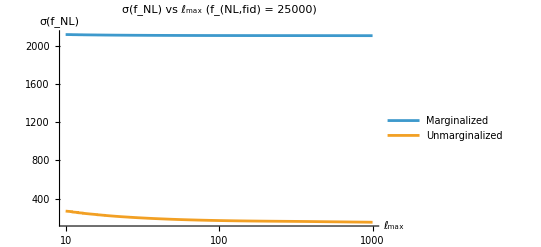

```mathematica
sigmaplotter[lvar_]:=Sqrt[Inverse[Table[Sum[D[cμT[q],params[[x]]]*D[cμT[q],params[[y]]]/((Sqrt[1/(2q+1)*cTT[q]*(w^(-1)*Exp[(q/lvar)^2])])^2),{q,2,lvar}],{x,1,n},{y,1,n}]+prior][[1,1]]/.{ns->nsfid,fNL->fNLfid}]
UMsigmaplotter[lvar_] :=1/Sqrt[(Table[Sum[D[cμT[q],params[[x]]]*D[cμT[q],params[[y]]]/((Sqrt[1/(2q+1)*cTT[q]*(w^(-1)*Exp[(q/lvar)^2])])^2),{q,2,lvar}],{x,1,n},{y,1,n}]+prior)[[1,1]]]/.{ns->nsfid,fNL->fNLfid}
LogLinearPlot[{sigmaplotter[lmaxvar],UMsigmaplotter[lmaxvar]},{lmaxvar,10,999},PlotRange->{0,All},PlotLabel->Row[{"σ(\!\(\*SubscriptBox[\(f\), \(NL\)]\)) vs ",Subscript[ℓ,"max"],"   (\!\(\*SubscriptBox[\(f\), \(NL,fid\)]\) = ",fNLfid,")"}],AxesLabel->{"\!\(\*SubscriptBox[\\(ℓ\\), \(max\)]\)","σ(\!\(\*SubscriptBox[\(f\), \(NL\)]\))"},PlotLegends->Placed[LineLegend[{"Marginalized","Unmarginalized"},LabelStyle->{FontSize->10}],{Left,Center}]]
```

```mathematica
G = Inverse[Inverse[FDLogL]]/.{ns->nsfid,fNL->fNLfid}

(*coplot =ContourPlot[{G[[1,1]](fNL-fNLfid)^2+2G[[1,2]](fNL-fNLfid)*(ns-nsfid)+G[[2,2]](ns-nsfid)^2 ==1/.434},{fNL,-50000,50000},{ns,-10*nsfid,10*nsfid},PlotRange->Automatic,PlotPoints->90,MaxRecursion->7,AxesLabel->{Subscript["n","s"],Subscript["f","NL"]},PlotLabel->Row[{Subscript["n","s"]," vs ",Subscript["f","NL"],"  1-σ and 2-σ contour plot"}]]
coplot2 = ContourPlot[{G[[1,1]](fNL-fNLfid)^2+2G[[1,2]](fNL-fNLfid)*(ns-nsfid)+G[[2,2]](ns-nsfid)^2 ==1/.167},{fNL,-50000,50000},{ns,-10*nsfid,10*nsfid},PlotRange->Automatic,PlotPoints->90,MaxRecursion->7,ContourStyle->Orange]
Show[coplot,coplot2,PlotRange->Automatic,PlotPoints->150,MaxRecursion->9,AxesLabel->{Subscript["n","s"],Subscript["f","NL"]},PlotLabel->Row[{Subscript["n","s"]," vs ",Subscript["f","NL"],"  1-σ and 2-σ contour plot (\!\(\*SubscriptBox[\(f\), \(NL,fid\)]\) = ",fNLfid,")"}],PlotLegends->{"1σ"}]*)

ContourPlot[{G[[1,1]](fNL-fNLfid)^2+2G[[1,2]](fNL-fNLfid)*(ns-nsfid)+G[[2,2]](ns-nsfid)^2 ==1/.434,G[[1,1]](fNL-fNLfid)^2+2G[[1,2]](fNL-fNLfid)*(ns-nsfid)+G[[2,2]](ns-nsfid)^2 ==1/.167},{fNL,-1000,4000},{ns,0.5,1.5*nsfid},PlotRange->Automatic,PlotPoints->1350,MaxRecursion->7,FrameLabel->{Subscript["f","NL"],Subscript["n","s"]},PlotLabel->Row[{Subscript["n","s"]," vs ",Subscript["f","NL"],"  1-σ and 2-σ contour plot (\!\(\*SubscriptBox[\(f\), \(NL,fid\)]\) = ",fNLfid,")"}],PlotLegends->Placed[{"1σ","2σ"},{Left,Bottom}]]
```

{{0.0000330647,17.3497},{17.3497,9.16618×10^6}}

-Graphics-